# BigWham Verifications - 3DT6 Kernel

## Penny-shaped crack under uniform and shear loading

## Load Library

```mathematica
PacletDirectoryLoad[NotebookDirectory[]<>"../../../../"]
<<BigWhamLink`
GetFilesDate[]
```

{/Users/alexis/BigWhamLink/}

BigWhamLink`LTemplate`Classes`

{/Users/alexis/BigWhamLink/BigWhamLink/Kernel/../LibraryResources/MacOSX-x86-64/HmatExpressions.dylib→Sat 13 Feb 2021 00:14:11GMT+1,/Users/alexis/bigwham_c4s/cmake-build-release/libBigWham.a→Sat 13 Feb 2021 00:00:01GMT+1}

## Mesh

### Mesh NDSolve FEM

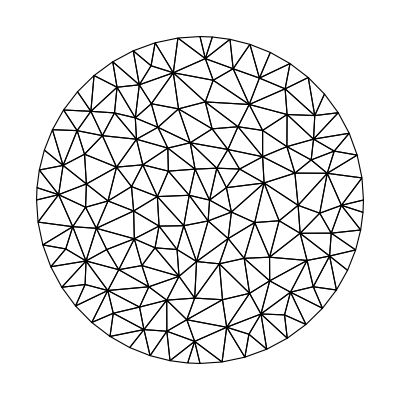

Number of Elements:252

```mathematica
Needs["NDSolve`FEM`"]
R=1;
maxCellMeasure=0.02;
Ω=Disk[{0,0},R];
mesh=ToElementMesh[Ω,"MeshOrder"->1,MaxCellMeasure->maxCellMeasure];
coorVerticesXY=mesh["Coordinates"];
coorVerticesXYZ=MapThread[Append,{coorVerticesXY,ConstantArray[0,Length[coorVerticesXY]]}];
conn=mesh["MeshElements"][[1]][[1]];
Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXY,Polygon[conn]]}]]
numberElements=Dimensions[conn,1][[1]];
Labeled["Number of Elements:",numberElements]
```

```mathematica
(* --- inputs for running tests in main.cpp of bigwham, C++ side --- *)

Export[NotebookDirectory[]<>"vertices.csv",coorVerticesXYZ,"CSV"]
Export[NotebookDirectory[]<>"conn.csv",conn-1,"CSV"]
```

/Users/alexis/BigWhamLink/vertices.csv

/Users/alexis/BigWhamLink/conn.csv

## Mesh utilities

### Rotation matrices

```mathematica
computeRotationMatrix[y1_List,y2_List,y3_List]:=Module[
{tangent1,normal,tangent2,rotMat},
tangent1=y2-y1;
tangent1=tangent1/Norm[tangent1];
normal=Cross[tangent1,y3-y1];
normal=normal/Norm[normal];
tangent2=Cross[normal,tangent1];
rotMat={tangent1,tangent2,normal}
];

allRotMat=Table[
computeRotationMatrix[
coorVerticesXYZ[[conn[[i,1]]]],
coorVerticesXYZ[[conn[[i,2]]]],
coorVerticesXYZ[[conn[[i,3]]]]],
{i,numberElements}];
```

## Build H-mat

```mathematica
ker="3DT6";
G=1;ν=0.25;Young=2G(1+ν);λ=(Young ν)/((1+ν)(1-2 ν));
maxleaf=100;
eta=10.;
eps=0.0001;
```

```mathematica
h1=toHMatExpr[coorVerticesXYZ,conn,ker,{Young,ν},maxleaf,eta,eps];//AbsoluteTiming
```

constructor called

Now setting up and constructing the HMatrix ...

HMatrix is now set !

{9.80909,Null}

```mathematica
GetCompressionRatio[h1]
GetSize[h1]
numberUnknowns=GetSize[h1][[1]]
numberCollocationPoints=numberUnknowns/3
```

0.488535

{4536,4536}

4536

1512

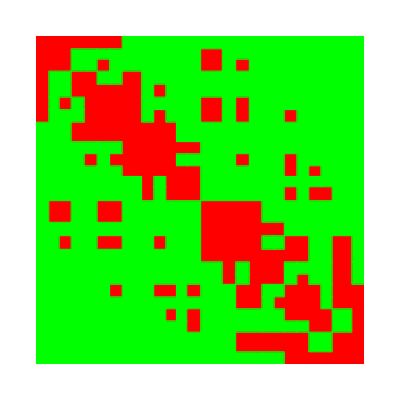

```mathematica
PlotHpattern[h1]
```

## Verification

### Compute coordinates of nodes (DD) and collocation points (traction)

#### Nodes for 3DT6

```mathematica
(* --- coordinates of nodes for 3DT6 --- *)

computeNodesCoordinates[y1_List,y2_List,y3_List]:=Module[
{coorNodes},
coorNodes=ConstantArray[0.,{6,3}];
coorNodes[[1]]=y1;coorNodes[[2]]=y2;coorNodes[[3]]=y3;
(*Same convention that C++ for middle edge nodes*)
coorNodes[[4]]=(y2+y3)/2;
coorNodes[[5]]=(y1+y3)/2;
coorNodes[[6]]=(y1+y2)/2;
coorNodes
];
coorNodesXYZ=Table[
computeNodesCoordinates[
coorVerticesXYZ[[conn[[i,1]]]],
coorVerticesXYZ[[conn[[i,2]]]],
coorVerticesXYZ[[conn[[i,3]]]]],
{i,numberElements}];
coorNodesXYZ=Flatten[coorNodesXYZ,1];
```

#### Collocation points

```mathematica
(* --- collocation points for any kernel --- *)
(* be careful, they are permuted !! *)

coorCollXYZ=GetCollocationPoints[h1];
```

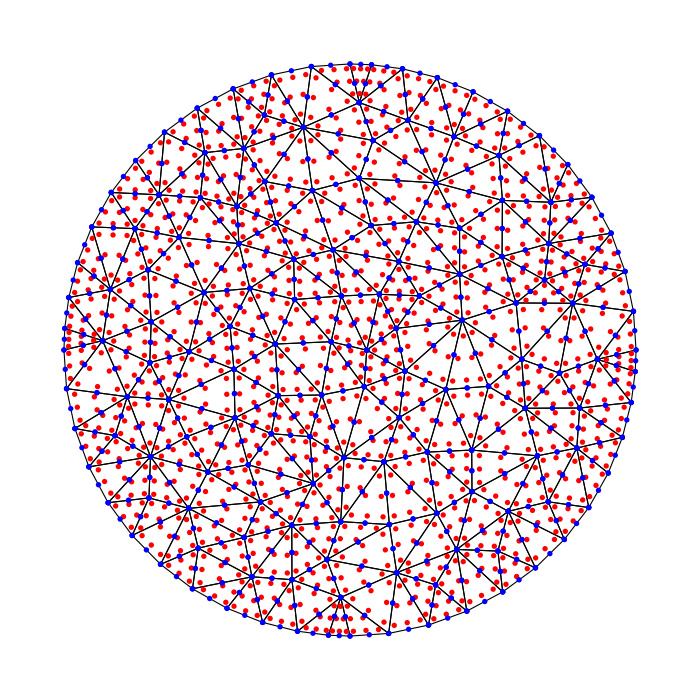

```mathematica
Show[Graphics[{EdgeForm[Black],FaceForm[],GraphicsComplex[coorVerticesXYZ[[;;,1;;2]],Polygon[conn]]}],
ListPlot[coorCollXYZ[[;;,1;;2]],PlotStyle-> Red],
ListPlot[coorNodesXYZ[[;;,1;;2]],PlotStyle-> Blue],ImageSize-> 700]
```

## Analytical solution

#### Select direction of loading

```mathematica
comp=1;(*{1,2,3}={shear1,shear2,normal}*)
```

#### Radial coordinate of nodes (DD) and collocation points

```mathematica
rNodes=Norm[#]&/@coorNodesXYZ[[;;,1;;2]];
rColl=Norm[#]&/@coorCollXYZ[[;;,1;;2]];
```

#### Analytical solutions functions

```mathematica
P=1; (*Uniform stress magnitude*)
DDsneddon[r_]:=(8 P)/(π (Young/(1-ν^2))) √Abs[R^2-r^2];
DDsegedin[r_]:=(8 (λ+2G) P)/(π G(3 λ+4G)) √Abs[R^2-r^2];

DDanalytical=ConstantArray[0.,numberUnknowns];

If[comp==3,
DDanalytical[[3;;-1;;3]]=DDsneddon[#]&/@rNodes,
DDanalytical[[comp;;-1;;3]]=DDsegedin[#]&/@rNodes];
```

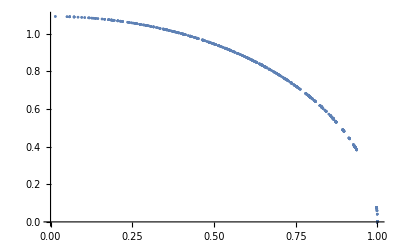

```mathematica
ListPlot[{rNodes,DDanalytical[[comp;;-1;;3]]}//Transpose]
```

```mathematica
(* --- express in local coordinate system if needed --- *)

(*for 3DT6*)

DDlocal=Table[
allRotMat[[Floor[(i-1)/6]+1]].DDanalytical[[3*(i-1)+1;;3*(i-1)+3]]
,{i,Length@coorCollXYZ}]//Flatten;
DDanalytical=DDlocal;
```

### Test H-dot only

```mathematica
tractionNumerical=Hdot[h1,DDanalytical];//AbsoluteTiming
```

{0.012611,Null}

```mathematica
(* --- express in global coordinate system if needed --- *)

(*for 3DT6*)

tractionGlobal=Table[
Transpose@allRotMat[[Floor[(i-1)/6]+1]].tractionNumerical[[3*(i-1)+1;;3*(i-1)+3]]
,{i,Length@coorCollXYZ}]//Flatten;
tractionNumerical=tractionGlobal;
```

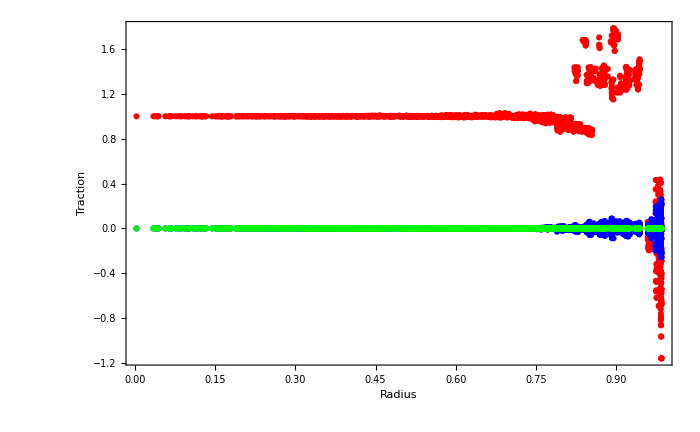

```mathematica
Show[
ListPlot[{rColl,tractionNumerical[[1;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rColl,tractionNumerical[[2;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Blue],
ListPlot[{rColl,tractionNumerical[[3;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Green],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radius","Traction"}), 
PlotRange-> All,ImageSize-> 700
]
```

### Test linear solve with H-dot

```mathematica
F=ConstantArray[0.,numberUnknowns];
F[[comp;;-1;;3]]=P;
fdot[x_?(VectorQ[#,NumericQ]&)]:=Hdot[h1,x];
```

```mathematica
(* --- express in local coordinate system if needed --- *)

(*for 3DT6*)

Flocal=Table[
allRotMat[[Floor[(i-1)/6]+1]].F[[3*(i-1)+1;;3*(i-1)+3]]
,{i,Length@coorCollXYZ}]//Flatten;
F=Flocal;
```

```mathematica
{sol,stats}=Reap@LinearSolve[fdot,F,Method->{"Krylov",{"Method"->"BiCGSTAB"(*"GMRES"*)(*"BiCGSTAB"*),(*"Preconditioner"->precJ,"PreconditionerSide"->Right,*)(*"StartingVector"->v0,*)"Tolerance"->10^-5.,"MaxIterations"->1000,"ResidualNormFunction"->((Sow[Norm[#,2]])&)}}];//AbsoluteTiming
```

{0.159492,Null}

```mathematica
(* --- express in global coordinate system if needed --- *)

(*for 3DT6*)

solGlobal=Table[
Transpose@allRotMat[[Floor[(i-1)/6]+1]].sol[[3*(i-1)+1;;3*(i-1)+3]]
,{i,Length@coorCollXYZ}]//Flatten;
sol=solGlobal;
```

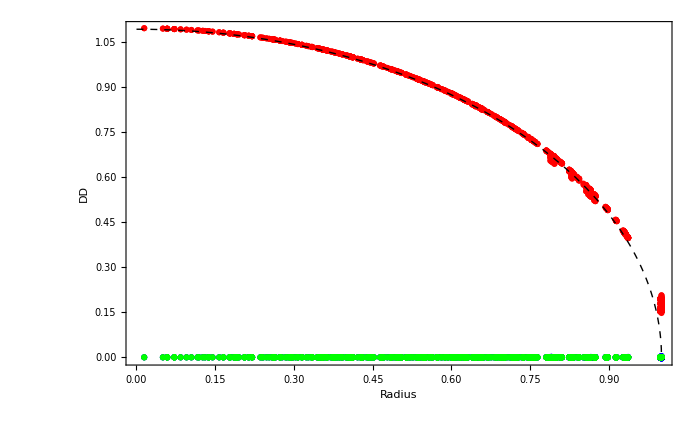

```mathematica
Show[
ListPlot[{rNodes,sol[[1;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Red],
ListPlot[{rNodes,sol[[2;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Blue],
ListPlot[{rNodes,sol[[3;;-1;;3]]}//Transpose,PlotMarkers->Automatic,PlotStyle->Green],
(*Plot[DDsneddon[x],{x,0,1},PlotStyle-> Red]*)
Plot[DDsegedin[x],{x,0,1},PlotStyle-> {Black,Dashed,Thick}],
Frame-> True,BaseStyle->{FontColor->Black,FontSize->22,FontFamily->"Times"},
FrameLabel->(Style[#,FontColor->Black,FontSize->25]& /@{"Radius","DD"}), 
PlotRange-> All,ImageSize-> 700]
```